```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
Rtor[R_]:=R-a^2/RH;
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
M=.;a=.;
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}];
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}];
christoffel[[2,1,1]]
christoffel[[2,1,1]] /. r-> 4 /. θ -> π/4
christoffel[[2,2,2]]  /. r-> 4 /. θ -> π/4
```

-(M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)

-((-16+a^2/2) (a^2+4 (4-2 M)) M)/((16+a^2/2)^3)

(4 (a^2-4 M)+1/2 a^2 (-4+M))/((16+a^2/2) (a^2+4 (4-2 M)))

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(r[τ]≤1.01*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
(* This one calculates u dot u *)
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
(* And this one prints out the coordinates *)
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
(* Define various plotting functions *)
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

```mathematica
τend=.;uinvar = 0;
rh=1.0;ct=-0.5;
M=(rh-2ct)/2.0
a = Sqrt[ct(ct-rh)](rh-2ct)/2
RH = M+Sqrt[M^2-a^2];
(* Since we are plotting in the BL space, the horizon is at RH, not rh *)
horizpl=PolarPlot[RH,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=100;
```

1.

0.866025

```mathematica
soln=computeSoln[τPlot,{-0.1,0,0.01},{0,8 RH,π/2,0}];
xyzsoln=sphslnToCartsln[soln];
Table[{τi,Rtor[coords[[2]][τ]/.soln/.τ->τi]},{τi,0,100,1}]
```

{{0,{11.5}},{1,{11.4005}},{2,{11.3019}},{3,{11.2043}},{4,{11.1078}},{5,{11.0122}},{6,{10.9178}},{7,{10.8244}},{8,{10.7321}},{9,{10.6409}},{10,{10.5509}},{11,{10.4621}},{12,{10.3745}},{13,{10.2881}},{14,{10.2031}},{15,{10.1193}},{16,{10.0368}},{17,{9.95565}},{18,{9.87591}},{19,{9.79758}},{20,{9.72069}},{21,{9.64527}},{22,{9.57135}},{23,{9.49897}},{24,{9.42815}},{25,{9.35892}},{26,{9.29132}},{27,{9.22537}},{28,{9.16111}},{29,{9.09856}},{30,{9.03777}},{31,{8.97875}},{32,{8.92154}},{33,{8.86618}},{34,{8.81268}},{35,{8.76108}},{36,{8.71141}},{37,{8.66369}},{38,{8.61796}},{39,{8.57424}},{40,{8.53256}},{41,{8.49294}},{42,{8.45541}},{43,{8.41999}},{44,{8.3867}},{45,{8.35558}},{46,{8.32662}},{47,{8.29987}},{48,{8.27533}},{49,{8.25302}},{50,{8.23295}},{51,{8.21515}},{52,{8.19962}},{53,{8.18637}},{54,{8.17542}},{55,{8.16677}},{56,{8.16042}},{57,{8.15639}},{58,{8.15467}},{59,{8.15527}},{60,{8.15818}},{61,{8.16341}},{62,{8.17094}},{63,{8.18078}},{64,{8.19292}},{65,{8.20735}},{66,{8.22405}},{67,{8.24302}},{68,{8.26424}},{69,{8.28771}},{70,{8.31339}},{71,{8.34128}},{72,{8.37136}},{73,{8.4036}},{74,{8.43799}},{75,{8.4745}},{76,{8.51311}},{77,{8.5538}},{78,{8.59653}},{79,{8.64129}},{80,{8.68805}},{81,{8.73678}},{82,{8.78745}},{83,{8.84003}},{84,{8.8945}},{85,{8.95082}},{86,{9.00896}},{87,{9.0689}},{88,{9.1306}},{89,{9.19403}},{90,{9.25917}},{91,{9.32598}},{92,{9.39442}},{93,{9.46447}},{94,{9.53611}},{95,{9.60929}},{96,{9.68398}},{97,{9.76016}},{98,{9.8378}},{99,{9.91686}},{100,{9.99732}}}

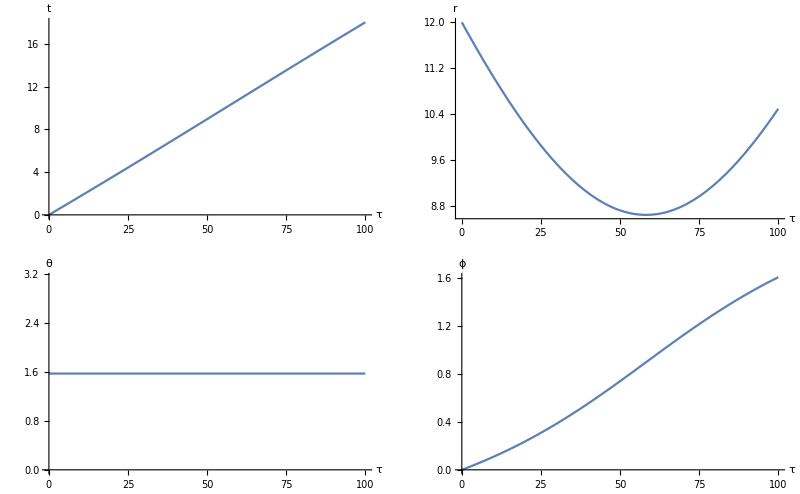

```mathematica
GraphicsGrid[{{Plot[{Evaluate[coords[[1]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","t"}],Plot[{Evaluate[coords[[2]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","r"}]},{Plot[{Evaluate[coords[[3]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","θ"}],Plot[{Evaluate[coords[[4]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","ϕ"}]}}]
```

The particle did not cross the horizon for initial coordinates={0,6.,π/2,0} and initial velocities={-0.1,0,0.01}

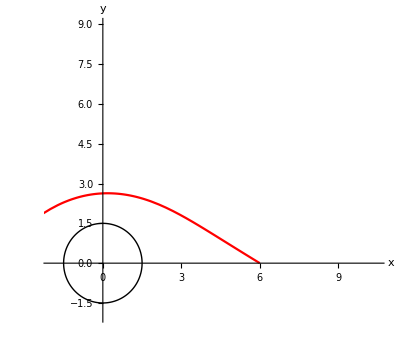

```mathematica
(* first one, in red, is other Kerr and the second one, in blue, is BL Kerr *)
genXYPlot[τPlot,{0,4 RH,π/2,0},{-0.1,0,0.01},1];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-2,7RH},{-2,6RH}}]
```

```mathematica
a
M
rh
ct
tt /. r -> 10 /. θ-> π/2
rr /. r -> 10 /. θ-> π/2
θθ /. r -> 10 /. θ-> π/2
ϕϕ /. r -> 10 /. θ-> π/2
```

0.866025

1.

1.

-0.5

-0.8

1.23839

100.

100.9